## Forbes & Beer (2024) - Minimal Modeling for Cognitive Ecologists: Measuring Decision-Making Trade-Offs in Ecological Tasks

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Use of Dynamica is required in this notebook. To use, download from https://rdbeer.pages.iu.edu/ and change this line to the correct directory *)
Quiet[<<"/Users/eden/Downloads/Dynamica.m"];
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
(* Specify Which Batch to Examine *)
opath = "menagerie/IndBatch2";
(* Specify Number of Files in Batch *)
numFiles = 100;
```

### 3N CTRNN & Import Functions

```mathematica
σ[x_]=1/(1+ⅇ^-x);
```

```mathematica
preyCTRNN=
DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w31 σ[y3+θ3]+sw11 d1+sw12 d2+sw13 d3)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w32 σ[y3+θ3]+sw21 d1+sw22 d2+sw23 d3)/τ2,
(-y3+w13 σ[y1+θ1]+w23 σ[y2+θ2]+w33 σ[y3+θ3]+sw31 d1+sw32 d2+sw33 d3)/τ3},
{{y1,-200,200},{y2,-200,200},{y3,-200,200}},
{{w11,-16,16},{w12,-16,16},{w13,-16,16},
{w21,-16,16},{w22,-16,16},{w23,-16,16},
{w31,-16,16},{w32,-16,16},{w33,-16,16},
{θ1,-16,16},{θ2,-16,16},{θ3,-16,16},
{τ1,0.5,20},{τ2,0.5,20},{τ3,0.5,20},
{sw11,-20,20},{sw12,-20,20},{sw13,-20,20},
{sw21,-20,20},{sw22,-20,20},{sw23,-20,20},
{sw31,-20,20},{sw32,-20,20},{sw33,-20,20},
{d1,-2,2},{d2,-2,2},{d3,0,3}
}];
```

```mathematica
With[{ε=10^-20},
preyOP=
TransformDynamicalSystem[preyCTRNN,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
importPrey[file_String,numNeurons_Integer]:=Module[{data,timeConstants,biases,weights,sensoryWeights},data=Flatten[Import[file,"Table"]];
timeConstants=data[[1;;numNeurons]];
biases=data[[numNeurons+1;;2*numNeurons]];
weights=Partition[data[[2*numNeurons+1;;2*numNeurons+numNeurons^2]],numNeurons];
sensoryWeights=data[[2*numNeurons+numNeurons^2+1;;5*numNeurons+numNeurons^2]];
preyCTRNN/.
{θ1->biases[[1]],τ1->timeConstants[[1]],
θ2->biases[[2]],τ2->timeConstants[[2]],
θ3->biases[[3]],τ3->timeConstants[[3]],
w11->weights[[1,1]],w12->weights[[1,2]],w13->weights[[1,3]],
w21->weights[[2,1]],w22->weights[[2,2]],w23->weights[[2,3]],
w31->weights[[3,1]],w32->weights[[3,2]],w33->weights[[3,3]],
sw11->sensoryWeights[[1]],sw12->sensoryWeights[[2]],sw13->sensoryWeights[[3]],
sw21->sensoryWeights[[4]],sw22->sensoryWeights[[5]],sw23->sensoryWeights[[6]],
sw31->sensoryWeights[[7]],sw32->sensoryWeights[[8]],sw33->sensoryWeights[[9]],
d1->0, d2->0, d3->0}]
```

## EA Plots (Multiple Phenotypes)

Code used to create plots of the evolutionary runs used in this study (see Figure 1).

```mathematica
CCtrials = 10;
evodatapop = List[];
successes = List[];
successlist = List[];
For[i=1,i<=numFiles,i++,
run = Import[ opath<>"/evolutions/evol_"<>ToString[i]<>".dat"];
BestInd = List[];
For[j=1,j<Length[run],j++,
AppendTo[BestInd,{run[[j]][[1]],run[[j]][[2]]}];
];
passes = Cases[run,{_,y_,_,_}/;y>=1.03];
If[Length[passes]>=CCtrials,
AppendTo[successes,BestInd];
AppendTo[successlist,i];
];
AppendTo[evodatapop,BestInd];
]
```

```mathematica
popevolfig = Show[ListPlot[evodatapop,Joined->True,ImageSize->Large,PlotRange->All, PlotStyle->{Lighter[Lighter[Gray]]}],
Graphics[{Dashed, Thick, Black, InfiniteLine[{{0,1},{50,1}}]}],
ImageSize->Large, LabelStyle->{16,Black},Frame->True,FrameLabel->{"Generation","Fitness"}];
```

```mathematica
successevolfig = Show[ListPlot[successes,Joined->True,ImageSize->Large,PlotRange->All, ColorFunction->"BlueGreenYellow"],
Graphics[{Dashed, Thick, Black, InfiniteLine[{{0,1},{50,1}}]}],
ImageSize->Large, LabelStyle->{16,Black},Frame->True,FrameLabel->{"Generation","Fitness"}];
successrate = Length[successes]/numFiles
successlist
```

11/50

{2,6,8,11,13,14,15,18,22,23,32,35,36,39,42,47,52,63,68,76,79,99}

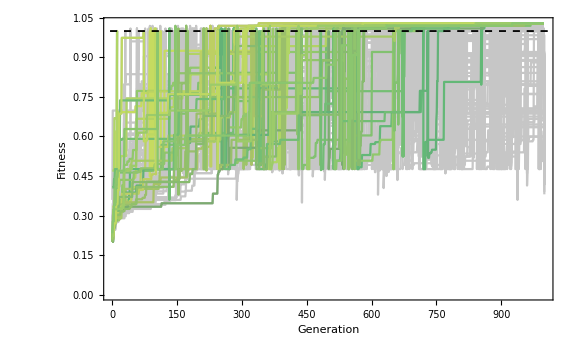

```mathematica
finalevolfig = Show[popevolfig,successevolfig, ImageSize->Large]
```

## Behavioral Traces (Single Phenotypes)

Code used to generate behavioral traces of the whole community (see Figure 2).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
chunkend =5000;
interval = 100;
predcondition = ToString[2];
```

```mathematica
For[i=1,i<Length[successlist],i++,
(* Set Agent Number *)
agent = ToString[successlist[[i]]];
(* Import Data *)
foodpos = Import[opath<>"/analysis_results/ns_"<>agent<>"/food_pos.dat"];
preypos = Import[opath<>"/analysis_results/ns_"<>agent<>"/prey_pos.dat"];
predpos = Import[opath<>"/analysis_results/ns_"<>agent<>"/pred_pos.dat"];
(* Chunk Data *)
preychunk = Part[preypos,Range[1,Length[preypos],interval]];
predchunk = Part[predpos,Range[1,Length[predpos],interval]];
foodchunk = Part[foodpos,Range[1,Length[foodpos],interval]];
(* Plot Traces *)
preyplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preychunk,PlotStyle->Blue];
predplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predchunk,PlotStyle->Red];
foodplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodchunk,PlotStyle->Darker[Green]];
(* Make Image *)
btraces = Show[
foodplot,
preyplot,
predplot,
PlotRange->{{0,3000},{0,5000}},ImageSize-> Large, AxesOrigin->{{0,0}},LabelStyle->20,Frame->True, FrameLabel->{"Time", "Position"}];
(* Export Image *)
Export[opath<>"/analysis_results/ns_"<>agent<>"/btraces_c"<>predcondition<>".jpg",btraces];
]
```

ListPlot::lpn: {{{1.,2069.},{1.,293.},{1.,2557.}},{{2.,2069.},{2.,293.},{2.,2557.}},{{3.,2069.},{3.,293.},{3.,2557.}},{{4.,2069.},{4.,293.},{4.,2557.}},{{5.,2069.},{5.,293.},{5.,2557.}},{{6.,2069.},{6.,293.},{6.,2557.}},{{7.,2069.},{7.,293.},{7.,2557.}},{{8.,2069.},{8.,293.},{8.,2557.}},{{9.,2069.},{9.,293.},{9.,2557.}},{{10.,2069.},{10.,293.},{10.,2557.}},«2990»} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

#### Original Pieces

```mathematica
foodpos = Import[opath<>"/analysis_results/ns_95/food_pos.dat"];
preypos = Import[opath<>"/analysis_results/ns_95/prey_pos.dat"];
predpos = Import[opath<>"/analysis_results/ns_95/pred_pos.dat"];
end = Length[preypos]
```

300000

```mathematica
chunkend =5000;
interval = 100;
preychunk = Part[preypos,Range[1,Length[preypos],interval]];
predchunk = Part[predpos,Range[1,Length[predpos],interval]];
foodchunk = Part[foodpos,Range[1,Length[foodpos],interval]];
```

```mathematica
preyplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preychunk,PlotStyle->Blue];
predplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predchunk,PlotStyle->Red];
foodplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodchunk,PlotStyle->Darker[Green]];
```

ListPlot::lpn: {{{1.,2069.},{1.,293.},{1.,2557.}},{{2.,2069.},{2.,293.},{2.,2557.}},{{3.,2069.},{3.,293.},{3.,2557.}},{{4.,2069.},{4.,293.},{4.,2557.}},{{5.,2069.},{5.,293.},{5.,2557.}},{{6.,2069.},{6.,293.},{6.,2557.}},{{7.,2069.},{7.,293.},{7.,2557.}},{{8.,2069.},{8.,293.},{8.,2557.}},{{9.,2069.},{9.,293.},{9.,2557.}},{{10.,2069.},{10.,293.},{10.,2557.}},«2990»} is not a list of numbers or pairs of numbers.

```mathematica
btraces = Show[
(*preyvisminplot,
preyvismaxplot,
predvisminplot,
predvismaxplot,*)
foodplot,
preyplot,
predplot,
PlotRange->{{0,3000},{0,5000}},ImageSize-> Large, AxesOrigin->{{0,0}},LabelStyle->20,Frame->True, FrameLabel->{"Time", "Position"}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[{{{1,2069},{1,293},{1,2557}},{{2,2069},{2,293},{2,2557}},{{3,2069},{3,293},{3,2557}},{{4,2069},{4,293},{4,2557}},{{5,2069},{5,293},{5,2557}},{{6,2069},{6,293},{6,2557}},{{7,2069},{7,293},{7,2557}},{{8,2069},{8,293},{8,2557}},{{9,2069},{9,293},{9,2557}},{{10,2069},{10,293},{10,2557}},{{11,2069},{11,293},{11,2557}},{{12,2069},{12,293},{12,2557}},{{13,2069},{13,293},{13,2557}},{{14,2069},{14,293},{14,2557}},{{15,2069},{15,293},{15,2557}},{{16,2069},{16,293},{16,2557}},{{17,2069},{17,293},{17,2557}},2966,{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},PlotStyle→RGBColor[0, Rational[2, 3], 0]],7,1]
 |  |  |  |

```mathematica
Export[opath<>"/analysis_results/ns_28/btraces_c1.jpg",btraces];
```

## Sensorimotor Surfaces (Single Phenotypes)

Code to generate decision-making schemas and neural traces imposed over those schemas (see Figures 3 & 4).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Quiet[<<"/Users/eden/Downloads/Dynamica.m"];
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
(* Sensorimotor Surface Function *)
SMS[SS0_,FS0_,PS0_, oX0_, oY0_]:= Module[{SSx = SS0, FSx = FS0, PSx = PS0, oXx = oX0, oYx = oY0},
Clear[SS,FS,PS];
SS = SSx;
FS = FSx;
PS = PSx;
oX = oXx;
oY = oYx;
root = EquilibriumPoints[prey/.{d3->SS,d1->FS,d2->PS}, Tries->10];
valX = root[[1]][[3]][[1]];
valY = root[[1]][[3]][[2]];
If[Length[root]>1,
op = 1000,
op = σ[valY+oY]-σ[valX+oX]
];
op
];
```

```mathematica
successlist = {15}
```

{15}

```mathematica
For[i=1,i<=Length[successlist],i++,
(* Set Agent Number *)
agent = ToString[successlist[[i]]];
(* Import Agent *)
prey = importPrey[opath<>"/nerves/best.ns_"<>agent<>".dat",3];
oX =  prey[[9]][[22]][[2]];
oY =  prey[[9]][[23]][[2]];
(* Make Density Plots *)
dp3 = DensityPlot[SMS[3.0,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, MaxRecursion->6,ImageSize->Large, LabelStyle->16];
dp15 = DensityPlot[SMS[1.5,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False,MaxRecursion->6, ImageSize->Large,LabelStyle->16];
dp1 = DensityPlot[SMS[0.1,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False,MaxRecursion->6,ImageSize->Large,LabelStyle->16];
(* Format Plots *)
sm3= Show[dp3,
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
sm15 = Show[dp15,
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
sm1 = Show[dp1,
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
(* Export Plots *)
Export[opath<>"/analysis_results/ns_"<>agent<>"/sm3.jpg",sm3];
Export[opath<>"/analysis_results/ns_"<>agent<>"/sm15.jpg",sm15];
Export[opath<>"/analysis_results/ns_"<>agent<>"/sm1.jpg",sm1];
];
```

Too many free parameters for EquilibriumPoints: {FS,PS}

Too many free parameters for EquilibriumPoints: {FS,PS}

Too many free parameters for EquilibriumPoints: {FS,PS}

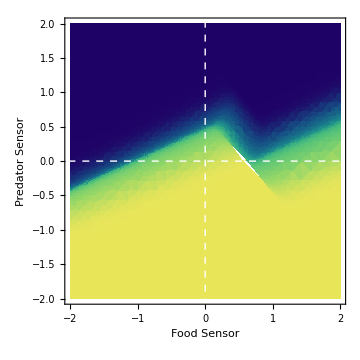

```mathematica
Show[sm15,
 Graphics[{Dashed, Thick,White, InfiniteLine[{{0,0},{50,0}}]}],
Graphics[{Dashed, Thick,White, InfiniteLine[{{0,0},{0,50}}]}],
ImageSize->Medium
]
```

```mathematica
GraphicsColumn[{sm3,sm15,sm1}, ImageSize->Large];
```

#### With Neural Trace

```mathematica
sensedat = Import[opath<>"/analysis_results/ns_15/SenSxx.dat"];
Length[sensedat[[1]]]
```

30001

```mathematica
pfsensampstart =23500;
pfsensampend =25500;
pffoodsamp = Take[sensedat[[1]],{pfsensampstart,pfsensampend}];
pfpredsamp = Take[sensedat[[5]],{pfsensampstart,pfsensampend}];
pfmovsamp = Take[sensedat[[16]],{pfsensampstart,pfsensampend}];
```

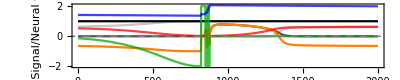

```mathematica
PredatorFoodNeuralTraces = Show[
ListPlot[Take[sensedat[[13]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Lighter[Lighter[Gray]]},AspectRatio->1/5, ImageSize->Full, PlotRange->All],
ListPlot[Take[sensedat[[14]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Darker[Gray]},AspectRatio->1/5, ImageSize->Full, PlotRange->All],
ListPlot[Take[sensedat[[15]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Black},AspectRatio->1/5, ImageSize->Full, PlotRange->All],
ListPlot[Take[sensedat[[16]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->Orange,AspectRatio->1/5, ImageSize->Full, PlotRange->All],
ListPlot[Take[sensedat[[5]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Red,Opacity[0.75]},AspectRatio->1/5, ImageSize->Full, PlotRange->All],
ListPlot[Take[sensedat[[1]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Darker[Green],Opacity[0.75]},AspectRatio->1/5, ImageSize->Full, PlotRange->All], 
ListPlot[Take[sensedat[[9]],{pfsensampstart,pfsensampend}], Joined -> True,PlotStyle->{Blue,Opacity[0.75]},AspectRatio->1/5, ImageSize->Full, PlotRange->All],
Graphics[{Dashed, Gray, InfiniteLine[{{0,0},{50,0}}]}],
PlotRange->All, AxesOrigin->{0,-2}, LabelStyle->20, Frame->True,FrameLabel->{"Time", "Input Signal/Neural Output"}
]
```

```mathematica
(* Import Data *)
foodpos = Import[opath<>"/analysis_results/ns_15/xx_food_pos.dat"];
preypos = Import[opath<>"/analysis_results/ns_15/xx_prey_pos.dat"];
predpos = Import[opath<>"/analysis_results/ns_15/xx_pred_pos.dat"];
(* Chunk Data *)
interval = 100;
preychunk = Part[preypos,Range[1,Length[preypos],interval]];
predchunk = Part[predpos,Range[1,Length[predpos],interval]];
foodchunk = Part[foodpos,Range[1,Length[foodpos],interval]];
(* Plot Traces *)
preyplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preychunk,PlotStyle->Blue];
predplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predchunk,PlotStyle->Red];
foodplot = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodchunk,PlotStyle->Darker[Green]];
(* Make Image *)
btraces = Show[
foodplot,
preyplot,
predplot,
PlotRange->All,ImageSize-> Large, AxesOrigin->{{0,0}},LabelStyle->20,Frame->True, FrameLabel->{"Time", "Position"}]
```

```mathematica
prezoomstart =23500;
prezoomend =24300;
postzoomstart =24350;
postzoomend =25500;
```

```mathematica
preyzoompre =Take[preypos,{prezoomstart,prezoomend}];
predzoompre =Take[predpos,{prezoomstart,prezoomend}];
foodzoompre =Take[foodpos,{prezoomstart,prezoomend}];
preyzoompost =Take[preypos,{postzoomstart,postzoomend}];
predzoompost =Take[predpos,{postzoomstart,postzoomend}];
foodzoompost =Take[foodpos,{postzoomstart,postzoomend}];
preyzoom =Take[preypos,{prezoomstart,postzoomend}];
predzoom =Take[predpos,{prezoomstart,postzoomend}];
foodzoom =Take[foodpos,{prezoomstart,postzoomend}];
```

```mathematica
preyplotpre = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preyzoompre,PlotStyle->Blue];
predplotpre = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predzoompre,PlotStyle->Red];
foodplotpre = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodzoompre,PlotStyle->Darker[Green]];
preyplotpost = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preyzoompost,PlotStyle->Blue];
predplotpost = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predzoompost,PlotStyle->Red];
foodplotpost = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodzoompost,PlotStyle->Darker[Green]];
preyplotzoom = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@preyzoom,PlotStyle->Blue];
predplotzoom = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@predzoom,PlotStyle->Red];
foodplotzoom = ListPlot[MapIndexed[Function[{value,index},{First@index,#}&/@value]]@foodzoom,PlotStyle->Darker[Green]];
```

```mathematica
btraceszoom = Show[
foodplotzoom,
preyplotzoom,
predplotzoom,
Graphics[{Dashed, Thick, Black, InfiniteLine[{{800,1},{800,5}}]}],
Graphics[{Dashed, Thick, Black, InfiniteLine[{{900,1},{900,5}}]}],
PlotRange->{{0,2000},{2700,3600}},ImageSize-> Full,AspectRatio->1/5, AxesOrigin->{{0,0}},LabelStyle->20,Frame->True, FrameLabel->{"Time", "Position"}]
```

```mathematica
GraphicsColumn[{PredatorFoodNeuralTraces,btraceszoom}, ImageSize->Full]
```

```mathematica
prefoodstart =23500;
prefoodend =24300;
prefoodsamp = Take[sensedat[[1]],{prefoodstart,prefoodend}];
prepredsamp = Take[sensedat[[5]],{prefoodstart,prefoodend}];
premovsamp = Take[sensedat[[16]],{prefoodstart,prefoodend}];
presplot = List[];
interval = 1;
prefoodchunk = Part[prefoodsamp,Range[1,Length[prefoodsamp],interval]];
prepredchunk = Part[prepredsamp,Range[1,Length[prepredsamp],interval]];
premovchunk = Part[premovsamp,Range[1,Length[premovsamp],interval]];
For[i=1,i<Length[prefoodchunk],i++,
point = List[];
AppendTo[point,prefoodchunk[[i]]];
AppendTo[point,prepredchunk[[i]]];
AppendTo[point,premovchunk[[i]]];
AppendTo[presplot,point];
]
```

```mathematica
PreSensorTrace = ListPlot[Style[#[[;;2]],ColorData["BlueGreenYellow"][Rescale[#[[3]],{-1,1}]]]&/@presplot,PlotStyle->{PointSize->0.02},Joined->True, AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
PreSensorTraceOutline = ListPlot[Style[#[[;;2]],ColorData["GrayTones"][Rescale[#[[3]],{-20,-10}]]]&/@presplot,PlotStyle->{PointSize->0.04},Joined->True, AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
```

```mathematica
PreSrfc = DensityPlot[SMS[1.35,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, MaxRecursion->6,ImageSize->Large];
```

Too many free parameters for EquilibriumPoints: {FS,PS}

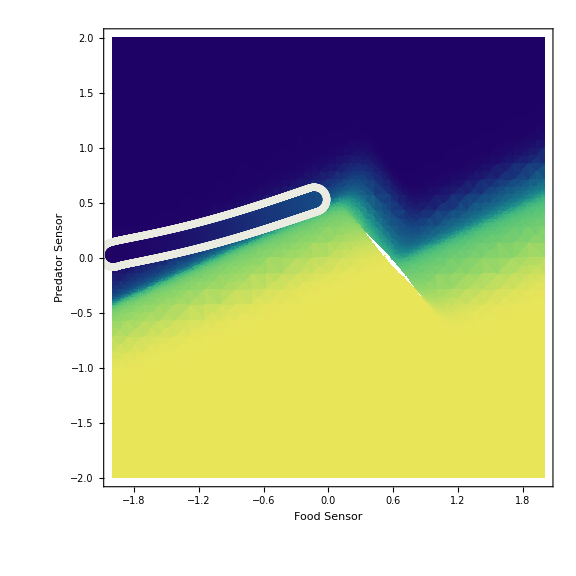

```mathematica
preplot = Show[PreSrfc,
PreSensorTraceOutline,
PreSensorTrace,
Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->24
]
```

```mathematica
feedstart =24300;
feedend =24350;
feedsamp = Take[sensedat[[1]],{feedstart,feedend}];
feedpredsamp = Take[sensedat[[5]],{feedstart,feedend}];
feedmovsamp = Take[sensedat[[16]],{feedstart,feedend}];
feedsplot = List[];
interval = 1;
feedchunk = Part[feedsamp,Range[1,Length[feedsamp],interval]];
feedpredchunk = Part[feedpredsamp,Range[1,Length[feedpredsamp],interval]];
feedmovchunk = Part[feedmovsamp,Range[1,Length[feedmovsamp],interval]];
For[i=1,i<Length[feedchunk],i++,
point = List[];
AppendTo[point,feedchunk[[i]]];
AppendTo[point,feedpredchunk[[i]]];
AppendTo[point,feedmovchunk[[i]]];
AppendTo[feedsplot,point];
]
```

```mathematica
FeedSensorTrace = ListPlot[Style[#[[;;2]],ColorData["BlueGreenYellow"][Rescale[#[[3]],{-1,1}]]]&/@feedsplot,PlotStyle->{PointSize->0.02},(*Joined->True,*) AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
FeedSensorTraceOutline = ListPlot[Style[#[[;;2]],ColorData["GrayTones"][Rescale[#[[3]],{-20,-10}]]]&/@feedsplot,PlotStyle->{PointSize->0.04},(*Joined->True,*) AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
```

```mathematica
FeedSrfc = DensityPlot[SMS[1.35,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, MaxRecursion->6,ImageSize->Large];
```

Too many free parameters for EquilibriumPoints: {FS,PS}

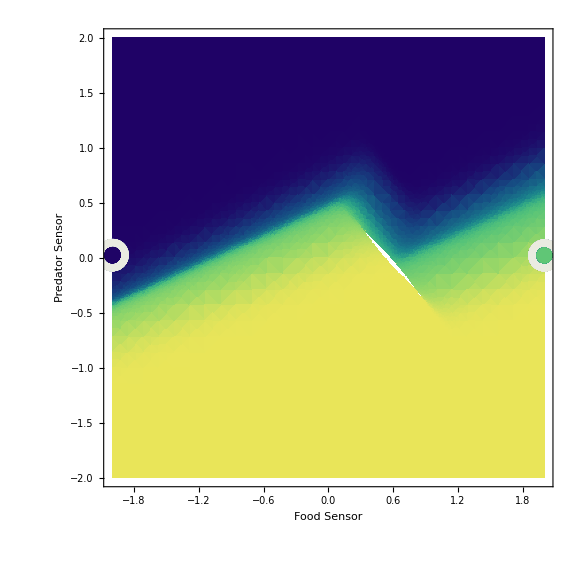

```mathematica
feedplot = Show[FeedSrfc,
FeedSensorTraceOutline,
FeedSensorTrace,
Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->24
]
```

```mathematica
postfoodstart =24400;
postfoodend =25500;
postfoodsamp = Take[sensedat[[1]],{postfoodstart,postfoodend}];
postpredsamp = Take[sensedat[[5]],{postfoodstart,postfoodend}];
postmovsamp = Take[sensedat[[16]],{postfoodstart,postfoodend}];
postsplot = List[];
interval = 1;
postfoodchunk = Part[postfoodsamp,Range[1,Length[postfoodsamp],interval]];
postpredchunk = Part[postpredsamp,Range[1,Length[postpredsamp],interval]];
postmovchunk = Part[postmovsamp,Range[1,Length[postmovsamp],interval]];
For[i=1,i<Length[postfoodchunk],i++,
point = List[];
AppendTo[point,postfoodchunk[[i]]];
AppendTo[point,postpredchunk[[i]]];
AppendTo[point,postmovchunk[[i]]];
AppendTo[postsplot,point];
]
```

```mathematica
PostSensorTrace = ListPlot[Style[#[[;;2]],ColorData["BlueGreenYellow"][Rescale[#[[3]],{-1,1}]]]&/@postsplot,PlotStyle->{PointSize->0.02},Joined->True, AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
PostSensorTraceOutline = ListPlot[Style[#[[;;2]],ColorData["GrayTones"][Rescale[#[[3]],{-20,-10}]]]&/@postsplot,PlotStyle->{PointSize->0.04},Joined->True, AspectRatio->1, PlotRange->{{-2,2},{-2,2}}, Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->16];
```

```mathematica
PostSrfc = DensityPlot[SMS[2.0,FS,PS, oX, oY], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, MaxRecursion->6,ImageSize->Large];
```

Too many free parameters for EquilibriumPoints: {FS,PS}

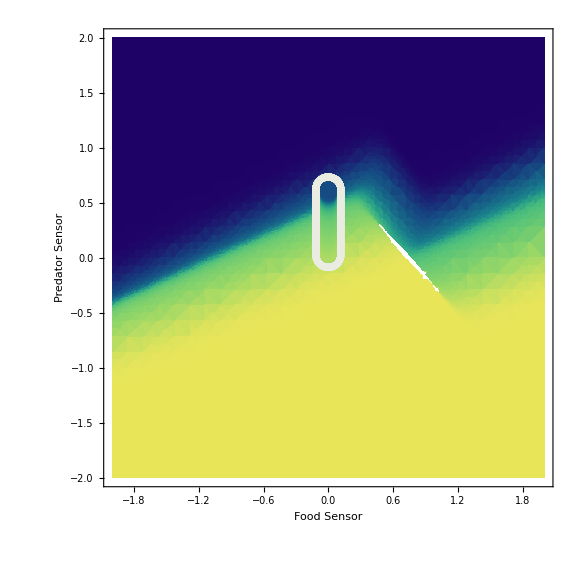

```mathematica
postplot = Show[PostSrfc,
PostSensorTraceOutline,
PostSensorTrace,
Frame->True, FrameLabel->{"Food Sensor", "Predator Sensor"}, LabelStyle->24
]
```

```mathematica
GraphicsRow[{preplot,feedplot,postplot}, ImageSize->Full];
```

### Original Pieces

```mathematica
prey = importPrey[opath<>"/nerves/best.ns_15.dat",3]
```

DynamicalSystem[«3 ODEs»,{y1,y2,y3},{d1→0,d2→0,d3→0,sw11→-8.08953,sw12→16.7966,sw13→-0.960004,sw21→7.13443,sw22→-18.154,sw23→-1.11643,sw31→-19.859,sw32→-11.745,sw33→5.64659,w11→-7.42003,w12→-14.8,w13→14.2061,w21→-11.8234,w22→-14.5084,w23→6.29344,w31→-12.239,w32→15.4472,w33→1.60394,θ1→9.10776,θ2→0.28392,θ3→-1.6876,τ1→0.648136,τ2→6.85607,τ3→14.6364}]

```mathematica
tX =  prey[[9]][[25]][[2]];
tY =  prey[[9]][[26]][[2]];
tZ =  prey[[9]][[27]][[2]];
W = {{ prey[[9]][[13]][[2]], prey[[9]][[14]][[2]], prey[[9]][[15]][[2]]},{ prey[[9]][[16]][[2]], prey[[9]][[17]][[2]], prey[[9]][[18]][[2]]},{ prey[[9]][[19]][[2]], prey[[9]][[20]][[2]], prey[[9]][[21]][[2]]}};
oX =  prey[[9]][[22]][[2]];
oY =  prey[[9]][[23]][[2]];
oZ = prey[[9]][[24]][[2]];
SW = {{prey[[9]][[4]][[2]],prey[[9]][[5]][[2]],prey[[9]][[6]][[2]]},{prey[[9]][[7]][[2]],prey[[9]][[8]][[2]],prey[[9]][[9]][[2]]},{ prey[[9]][[10]][[2]], prey[[9]][[11]][[2]], prey[[9]][[12]][[2]]}};
Clear[FS,PS,SS, X, Y, Z];
dX=1/tX(-X+W⟦1,1⟧σ[X+oX]+W⟦1,2⟧σ[Y+oY]+W⟦1,3⟧σ[Z+oZ]+SW[[1,1]]FS+ SW[[1,2]]PS+ SW[[1,3]]SS);
dY=1/tY(-Y+W⟦2,1⟧σ[X+oX]+W⟦2,2⟧σ[Y+oY]+W⟦2,3⟧σ[Z+oZ]+SW[[2,1]]FS+ SW[[2,2]]PS+ SW[[2,3]]SS);
dZ=1/tZ(-Z+W⟦3,1⟧σ[X+oX]+W⟦3,2⟧σ[Y+oY]+W⟦3,3⟧σ[Z+oZ]+SW[[3,1]]FS+ SW[[3,2]]PS+ SW[[3,3]]SS);
```

```mathematica
pc3 = DisplayParameterChart[prey/.{d3->3.0}, {d1,d2}, PlotRange->All, MaxSteps->Infinity];
pc15 = DisplayParameterChart[prey/.{d3->1.5}, {d1,d2}, PlotRange->All, MaxSteps->Infinity];
pc1 = DisplayParameterChart[prey/.{d3->0.1}, {d1,d2}, PlotRange->All, MaxSteps->Infinity];
```

```mathematica
dp3 = DensityPlot[SMS[3.0,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, MaxRecursion->6,ImageSize->Large];
dp15 = DensityPlot[SMS[1.5,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False,MaxRecursion->6, ImageSize->Large];
dp1 = DensityPlot[SMS[0.1,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False,MaxRecursion->6, ImageSize->Large];
```

```mathematica
sm3= Show[dp3,
(*ListLinePlot[pc3[[1]][[1]][[1]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc3[[1]][[1]][[2]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],*)
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
sm15 = Show[dp15,
(*ListLinePlot[pc15[[1]][[1]][[1]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc15[[1]][[1]][[2]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc15[[1]][[1]][[3]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc15[[1]][[1]][[4]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],*)
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
sm1 = Show[dp1,
(*ListLinePlot[pc1[[1]][[1]][[1]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc1[[1]][[1]][[2]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],
ListLinePlot[pc1[[1]][[1]][[3]][[2]][[1]], PlotStyle->{Lighter[Gray], Thickness->0.006}],*)
FrameLabel->{"Food Sensor","Predator Sensor"}, LabelStyle->16
];
```

```mathematica
Export[opath<>"/analysis_results/ns_77/sm3.jpg",sm3];
Export[opath<>"/analysis_results/ns_77/sm15.jpg",sm15];
Export[opath<>"/analysis_results/ns_77/sm1.jpg",sm1];
```

```mathematica
GraphicsRow[{sm3,sm15,sm1}, ImageSize->Full]
```

-Graphics-

#### Trade-Off Decomposition FUNCTION (State = 3.0)

```mathematica
Show[x3 = Plot3D[SMS[3.0,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->BarLegend[{"BlueGreenYellow", {-1,1}}]],
ContourPlot3D[x==0,{x,-2,2},{y,0,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,0,2},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[x==0,{x,-2,2},{y,-2,0},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,-2,0},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}]]
```

-Graphics3D-

```mathematica
SS = 3;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x3, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q1x3 = Show[Plot3D[SMS[3.0,FS,PS], {FS,0,2},{PS,0,2}, PlotRange->{{0,2},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ1x3, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x3, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x3 = Show[Plot3D[SMS[3.0,FS,PS], {FS,0,2},{PS,-2,0}, PlotRange->{{0,2},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ2x3, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x3, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x3 = Show[Plot3D[SMS[3.0,FS,PS], {FS,-2,0},{PS,-2,0}, PlotRange->{{-2,0},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ3x3, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x3, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x3 = Show[Plot3D[SMS[3.0,FS,PS], {FS,-2,0},{PS,0,2}, PlotRange->{{-2,0},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ4x3, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

#### Trade-Off Decomposition FUNCTION (State = 1.5)

```mathematica
Show[x15 = Plot3D[SMS[1.5,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->BarLegend[{"BlueGreenYellow", {-1,1}}]],
ContourPlot3D[x==0,{x,-2,2},{y,0,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,0,2},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[x==0,{x,-2,2},{y,-2,0},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,-2,0},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}]]
```

-Graphics3D-

```mathematica
SS = 1.5;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x15, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q1x15= Show[Plot3D[SMS[1.5,FS,PS], {FS,0,2},{PS,0,2}, PlotRange->{{0,2},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ1x15, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x15, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x15 = Show[Plot3D[SMS[1.5,FS,PS], {FS,0,2},{PS,-2,0}, PlotRange->{{0,2},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ2x15, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x15, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x15 = Show[Plot3D[SMS[1.5,FS,PS], {FS,-2,0},{PS,-2,0}, PlotRange->{{-2,0},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ3x15, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x15, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x15 = Show[Plot3D[SMS[1.5,FS,PS], {FS,-2,0},{PS,0,2}, PlotRange->{{-2,0},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ4x15, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

#### Trade-Off Decomposition FUNCTION (State = 0.1)

```mathematica
Show[x1 = Plot3D[SMS[0.1,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->BarLegend[{"BlueGreenYellow", {-1,1}}]],
ContourPlot3D[x==0,{x,-2,2},{y,0,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,0,2},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[x==0,{x,-2,2},{y,-2,0},{z,-1,1}, ContourStyle->{White, Opacity[0.8]}, Mesh->False, Lighting->{{"Ambient", White}}],
ContourPlot3D[y==0,{x,-2,0},{y,-2,2},{z,-1,1}, ContourStyle->{White, Opacity[0.8]},Mesh->False, Lighting->{{"Ambient", White}}]]
```

-Graphics3D-

```mathematica
SS = 0.1;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x1, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q1x1 = Show[Plot3D[SMS[0.1,FS,PS], {FS,0,2},{PS,0,2}, PlotRange->{{0,2},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ1x1, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x1, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x1 = Show[Plot3D[SMS[0.1,FS,PS], {FS,0,2},{PS,-2,0}, PlotRange->{{0,2},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ2x1, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x1, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x1 = Show[Plot3D[SMS[0.1,FS,PS], {FS,-2,0},{PS,-2,0}, PlotRange->{{-2,0},{-2,-0},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ3x1, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x1, {FS,PS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x1 = Show[Plot3D[SMS[0.1,FS,PS], {FS,-2,0},{PS,0,2}, PlotRange->{{-2,0},{0,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large,AxesLabel->{"Food Sensor","Predator Sensor","Motor Output"}],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray, Opacity[0.3]},Mesh->False, Lighting->{{"Ambient", White}}],
 ListPointPlot3D[TrajQ4x1, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

#### Collect DATA

```mathematica
(* Collect Data *)
rSS = Range[0,3,0.1];
rPS = Range[-2,2,0.02];
rFS = Range[-2,2,0.02];
PFto =  List[];
For [h =1, h<Length[rSS],h++,
SS = rSS[[h]];
SMfp = List[];
For[i=1,i<Length[rPS],i++,
For[j=1, j<Length[rFS],j++;
PS =rPS[[i]];
FS = rFS[[j]];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
valX = root[[1]][[2]];
valY = root[[2]][[2]];
AppendTo[SMfp, {PS,FS,σ[valY+oY]-σ[valX+oX]}]]];
AppendTo[PFto, SMfp]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

#### Trade-Off Decomposition DATA (State = 3.0)

```mathematica
Show[x3 = ListPointPlot3D[PFto[[30]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,2},{-2,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[x==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False],
ContourPlot3D[y==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False]]
```

-Graphics3D-

```mathematica
SS = 3;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x3, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q1x3 = Show[ListPointPlot3D[PFto[[30]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.0}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ1x3, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x3, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x3 = Show[ListPointPlot3D[PFto[[30]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ2x3, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x3, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x3 = Show[ListPointPlot3D[PFto[[30]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ3x3, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x3 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x3, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x3 = Show[ListPointPlot3D[PFto[[30]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ4x3, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

#### Trade-Off Decomposition DATA (State = 1.5)

```mathematica
Show[x15 = ListPointPlot3D[PFto[[15]],PlotStyle->{PointSize[Small]}, PlotRange->All, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[x==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False],
ContourPlot3D[y==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False]]
```

-Graphics3D-

```mathematica
SS = 1.5;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x15, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Q1x15 = Show[ListPointPlot3D[PFto[[15]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.0}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ1x15, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
SS = 1.5;
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x15, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x15 = Show[ListPointPlot3D[PFto[[15]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ2x15, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x15 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x15, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x15 = Show[ListPointPlot3D[PFto[[15]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ3x15, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x15=  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x15, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x15 = Show[ListPointPlot3D[PFto[[15]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ4x15, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

#### Trade-Off Decomposition DATA (State = 0.1)

```mathematica
Show[x1 = ListPointPlot3D[PFto[[1]],PlotStyle->{PointSize[Small]}, PlotRange->All, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[x==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False],
ContourPlot3D[y==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{White,Opacity[0.5]}, Mesh->False]]
```

-Graphics3D-

```mathematica
SS = 0.1;
FS = 1;
PS = 0;
r = Range[0,2,0.001];
TrajQ1x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ1x1, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Q1x1 = Show[ListPointPlot3D[PFto[[1]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.0}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ1x1, PlotRange->All, PlotStyle->Orange]
]
```

-Graphics3D-

```mathematica
FS = 1;
PS = -2;
r = Range[0,2,0.001];
TrajQ2x1=  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = 1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ2x1, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q2x1 = Show[ListPointPlot3D[PFto[[1]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{0,2},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ2x1, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = -2;
r = Range[0,2,0.001];
TrajQ3x1 =  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = -2+r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ3x1, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q3x1 =Show[ListPointPlot3D[PFto[[1]],PlotStyle->{PointSize[Small]}, PlotRange->{{-2,0},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ3x1, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

```mathematica
FS = -1;
PS = 0;
r = Range[0,2,0.001];
TrajQ4x1=  List[];
root = FindRoot[{dX==0,dY==0,dZ==0},{{X,0},{Y,0},{Z,0}}];
X = root[[1]][[2]];
Y = root[[2]][[2]];
Z = root[[3]][[2]];
For[i=1,i<Length[r],i++,
FS = -1;
PS = r[[i]];
X = X+ dX;
Y = Y + dY;
Z = Z+dZ;
AppendTo[TrajQ4x1, {PS,FS,σ[Y+oY]-σ[X+oX]}]];
```

```mathematica
Q4x1 = Show[ListPointPlot3D[PFto[[1]],PlotStyle->{PointSize[Small]}, PlotRange->{{0,2},{-2,0},{-1,1}}, AxesLabel->{"Predator Sensor","Food Sensor","Motor Output"}, AxesStyle->12,ViewPoint->{2.0, -2.0, 1.}, ImageSize->Large],
ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-1,1}, ContourStyle->{Gray,Opacity[0.1]}, Mesh->False],
 ListPointPlot3D[TrajQ4x1, PlotRange->All, PlotStyle->Orange]]
```

-Graphics3D-

#### Comparison Plots

```mathematica
GraphicsRow[{x3,x15,x1}, ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsRow[{Q1x3,Q1x15,Q1x1}, ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsRow[{Q2x3,Q2x15,Q2x1}, ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsRow[{Q3x3,Q3x15,Q3x1}, ImageSize->Full]
```

-Graphics-

```mathematica
GraphicsRow[{Q4x3,Q4x15,Q4x1}, ImageSize->Full]
```

-Graphics-

#### Animations (Data & Function)

```mathematica
S0 = Plot3D[SMS[0.1,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.1",ImageSize->Large];
S1 = Plot3D[SMS[0.2,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.2",ImageSize->Large];
S2 = Plot3D[SMS[0.3,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.3",ImageSize->Large];
S3 = Plot3D[SMS[0.4,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.4",ImageSize->Large];
S4 = Plot3D[SMS[0.5,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.5",ImageSize->Large];
S5 = Plot3D[SMS[0.6,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.6",ImageSize->Large];
S6 = Plot3D[SMS[0.7,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.7",ImageSize->Large];
S7 = Plot3D[SMS[0.8,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.8",ImageSize->Large];
S8 = Plot3D[SMS[0.9,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 0.9",ImageSize->Large];
S9 = Plot3D[SMS[1.0,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.0",ImageSize->Large];
S10 = Plot3D[SMS[1.1,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.1",ImageSize->Large];
S11 = Plot3D[SMS[1.2,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.2",ImageSize->Large];
S12 = Plot3D[SMS[1.3,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.3",ImageSize->Large];
S13 = Plot3D[SMS[1.4,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.4",ImageSize->Large];
S14 = Plot3D[SMS[1.5,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.5",ImageSize->Large];
S15 = Plot3D[SMS[1.6,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.6",ImageSize->Large];
S16 =Plot3D[SMS[1.7,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.7",ImageSize->Large];
S17 = Plot3D[SMS[1.8,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.8",ImageSize->Large];
S18 = Plot3D[SMS[1.9,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 1.9",ImageSize->Large];
S19 =Plot3D[SMS[2.0,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.0",ImageSize->Large];
S20 = Plot3D[SMS[2.1,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.1",ImageSize->Large];
S21 = Plot3D[SMS[2.2,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.2",ImageSize->Large];
S22 = Plot3D[SMS[2.3,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.3",ImageSize->Large];
S23 = Plot3D[SMS[2.4,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.4",ImageSize->Large];
S24 = Plot3D[SMS[2.5,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.5",ImageSize->Large];
S25 = Plot3D[SMS[2.6,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.6",ImageSize->Large];
S26 =Plot3D[SMS[2.7,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.7",ImageSize->Large];
S27 = Plot3D[SMS[2.8,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.8",ImageSize->Large];
S28 =Plot3D[SMS[2.9,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 2.9",ImageSize->Large];
S29 = Plot3D[SMS[3.0,FS,PS], {FS,-2,2},{PS,-2,2}, PlotRange->{{-2,2},{-2,2},{-1,1}},ViewPoint->{-2.0, 2.0, 1.2}, AxesEdge->{{-1,1},{1,1},{1,1}},Mesh->True,MeshStyle->White,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#3,{-1,1}]]&),ColorFunctionScaling->False, PlotLabel -> "State = 3.0",ImageSize->Large];
Slist = List[S0,S1,S2,S3,S4,S5,S6,S7,S8,S9,S10,S11,S12,S13,S14,
S15,S16,S17,S18,S19,S20,S21,S22,S23,S24,S25,S26,S27,S28,S29];
```

```mathematica
Sani = ListAnimate[Slist, 7];
```

```mathematica
Export["3DSM.gif",Sani];
```

$Aborted

```mathematica
T0 =DensityPlot[SMS[0.1,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.1",LabelStyle->16];
T1 = DensityPlot[SMS[0.2,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.2",LabelStyle->16];
T2 = DensityPlot[SMS[0.3,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.3",LabelStyle->16];
T3 = DensityPlot[SMS[0.4,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.4",LabelStyle->16];
T4 = DensityPlot[SMS[0.5,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.5",LabelStyle->16];
T5 = DensityPlot[SMS[0.6,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.6",LabelStyle->16];
T6 = DensityPlot[SMS[0.7,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.7",LabelStyle->16];
T7 = DensityPlot[SMS[0.8,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.8",LabelStyle->16];
T8 =DensityPlot[SMS[0.9,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 0.9",LabelStyle->16];
T9 =DensityPlot[SMS[1.0,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.0",LabelStyle->16];
T10 = DensityPlot[SMS[1.1,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.1",LabelStyle->16];
T11 =DensityPlot[SMS[1.2,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.2",LabelStyle->16];
T12 = DensityPlot[SMS[1.3,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.3",LabelStyle->16];
T13 =DensityPlot[SMS[1.4,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.4",LabelStyle->16];
T14 =DensityPlot[SMS[1.5,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.5",LabelStyle->16];
T15 =DensityPlot[SMS[1.6,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.6",LabelStyle->16];
T16 = DensityPlot[SMS[1.7,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.7",LabelStyle->16];
T17 =DensityPlot[SMS[1.8,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.8",LabelStyle->16];
T18 = DensityPlot[SMS[1.9,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 1.9",LabelStyle->16];
T19 =DensityPlot[SMS[2.0,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.0",LabelStyle->16];
T20 =DensityPlot[SMS[2.1,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.1",LabelStyle->16];
T21 = DensityPlot[SMS[2.2,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.2",LabelStyle->16];
T22 =DensityPlot[SMS[2.3,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.3",LabelStyle->16];
T23 =DensityPlot[SMS[2.4,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.4",LabelStyle->16];
T24 =DensityPlot[SMS[2.5,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.5",LabelStyle->16];
T25 = DensityPlot[SMS[2.6,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.6",LabelStyle->16];
T26 = DensityPlot[SMS[2.7,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.7",LabelStyle->16];
T27 =DensityPlot[SMS[2.8,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.8",LabelStyle->16];
T28 =DensityPlot[SMS[2.9,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 2.9",LabelStyle->16];
T29 =DensityPlot[SMS[3.0,FS,PS], {FS,-2,2},{PS,-2,2}, ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#1,{-1,1}]]&),ColorFunctionScaling->False, ImageSize->Large, PlotLegends->Automatic,FrameLabel->{"Food Sensor","Predator Sensor"},PlotLabel -> "State = 3.0",LabelStyle->16];
Tlist = List[T0,T1,T2,T3,T4,T5,T6,T7,T8,T9,T10,T11,T12,T13,T14,
T15,T16,T17,T18,T19,T20,T21,T22,T23,T24,T25,T26,T27,T28,T29];
```

```mathematica
Tani = ListAnimate[Tlist, 7];
```

```mathematica
Export["2DSM.gif",Tani];
```